# Runge-Kutta-Fehlberg Method

Last session we used a Runge-Kutta method, RK4, which is locally accurate to 5th order in step size, h^5, Globally accurate to 4th order h^4.
In this notebook, we’ve made some changes to explicitly treat time dependence.
For reference, this will look as follows in the Euler Forward case,

```mathematica
updateEF={f,h}↦state↦Module[{t=state[[1]],y=state[[2]]},{t+h,y+h f[t]@@y}];
```

We’ve set this up to take the time derivatives, i.e. the physics, with a function signature that partially applies time first then the phase space state vector.

```mathematica
f=t↦{θ,θp}↦{θp,-Sin[θ]-0.1 Sign[θp] θp^2};
```

The time-dependent RK4 function then looks like this. Note we partially apply f with each timestep before applying to the state vector.

```mathematica
updateRK4=Function[{f,h},Function[state,
Module[{k1,k2,k3,k4,y1,y2,y3,y4,t},
t=state[[1]];
y1=state[[2]];
k1=Apply[f[t],y1];
y2=y1+h/2 k1;
k2=f[t+h/2]@@y2;
y3=y1+h/2 k2;
k3=f[t+h/2]@@y3;
y4=y1+h k3;
k4=f[t+h]@@y4;
{t+h,y1+h (k1+2k2+2k3+k4)/6}
]
]];
```

## Animation

We can make an animation of our system by setting an initial state, constructing figures and setting them to dynamically update, and updating the state in a loop.
First set the initial state,

```mathematica
state={0,{-3.π,3}};
```

Then draw the figures we want to animate and run a loop to update the figures. (Use Alt-. to stop the animation once running.)

```mathematica
Dynamic@ParametricPlot[{r Sin[state[[2,1]]],-r Cos[state[[2,1]]]},{r,0,1},PlotStyle->Black,Epilog->{PointSize[Large],Red,Point[{Sin[state[[2,1]]],-Cos[state[[2,1]]]}]},PlotRange->{{-1.1,1.1},{-1.1,1.1}},AspectRatio->1]
Dynamic@Show[StreamPlot[f[0][θ,θp],{θ,-2π,2π},{θp,-π,π},
AspectRatio->1/2,GridLines->{{-π,0,π},{0}},PlotRangePadding->None,ImageSize->Large,
FrameLabel->{"Angle – θ", "Angular Velocity – θ'"}
],Epilog->{PointSize[Large],Red,Point[Last[state]]}]
Dynamic@state

step=updateRK4[f,0.1];
While[True,
state=step[state];
Pause[1/60];
]
```

$Aborted

## Runge-Kutta-Fehlberg

The RK4 method takes four function evaluations (of f) to compute. It is locally 5th order in timestep.
We set a timestep small enough to ensure a manageably small error, however it would be more favourable to set a tolerable error in the output and take the largest step size that will achieve this.
The issue is we don’t know what the error is on the RK4 method by itself. However if we could calculate an RK5 approximation, locally 6th order, then we could subtract the two to find the leading order error term. This is the truncation error, TE, i.e.,

(y(t+h))_RK4=(y(t+h))_exact+ε h^5+𝒪(h^6)
(y(t+h))_RK5=(y(t+h))_exact+η h^6+𝒪(h^7)

⇒ TE=(y(t+h))_RK4-(y(t+h))_RK5=ε h^5+𝒪(h^6)

If the truncation error is within a predefined tolerance, then we keep the calculation, and move onto the next, otherwise we redo the calculation with a smaller step size.
In both cases, we can calculate the size of the next step by, combining,
Tol ≃ε h_next^5, with,
(y(t+h))_RK4-(y(t+h))_RK5≃ε h^5
to return,
h_next=h (Tol/((y(t+h))_RK4-(y(t+h))_RK5))^(1/5)

This on face value seems inefficient, we need to do 4 function evaluations (of f) to calculate the next RK4 step and 5 to calculate the next RK5 step, meaning 9 function evaluations in total.
The Fehlberg modification to the scheme is to use a variant of RK4 that takes 5 function evaluations but with a degree of freedom on its coefficients, and a RK5 that similarly takes 6 function evaluations, and use the extra degree of freedom such that the 5 function evaluations in the RK4 are the same as are needed in the RK5.
In this case, we can calculate both RK4 and RK5 with only 6 function evaluations in total. This is more than the 4 needed for the usual RK4, but it allows us to set an adaptive step size and control the size of our error.

Method | Points | Local Error | Global Error
RK4 | 4 | h^5 | h^4
RK5 | 5 | h^6 | h^5
RK4 custom coeffs | 5 | h^5 | h^4
RK5 custom coeffs | 6 | h^6 | h^5

The RK methods with custom coefficients use a further modification where when calculating the y state values, all f values previously calculated are used in a weighted sum, rather than just the last one.
The Runge-Kutta-Fehlberg method (And the RKF45 version presented below) uses coefficients found by Fehlberg that solves the constraints of having RK4 and RK5 evaluate gradients at the same points in state space.

```mathematica
updateRKF45prime=Function[{f,tol},Function[state,
Module[{k1,k2,k3,k4,k5,k6,y1,y2,y3,y4,y5,y6,t,yNext,yHat,α,β,c,cHat,cTE,h,TE,hNext},
β=N[{{2/9, 0, 0, 0, 0}, {1/12, 1/4, 0, 0, 0}, {69/128, -243/128, 135/64, 0, 0}, {-17/12, 27/4, -27/5, 16/15, 0}, {65/432, -5/16, 13/16, 4/27, 5/144}}];
α=Total/@β;
c={1/9,0,9/20,16/45,1/12,0};
cHat={47/450,0,12/25,32/225,1/30,6/25};
cTE=c-cHat;
t=state[[1]];
y1=state[[2]];
h=state[[3]];
k1=Apply[f[t],y1];
y2=y1+β[[1,1]]h k1;
k2=f[t+α[[1]]h]@@y2;
y3=y1+β[[2,1]]h k1+β[[2,2]]h k2;
k3=f[t+α[[2]]h]@@y3;
y4=y1+β[[3,1]]h k1+β[[3,2]]h k2+β[[3,3]]h k3;
k4=f[t+α[[3]]h]@@y4;
y5=y1+β[[4,1]]h k1+β[[4,2]]h k2+β[[4,3]]h k3+β[[4,4]]h k4;
k5=f[t+α[[4]]h]@@y5;
y6=y1+β[[5,1]]h k1+β[[5,2]]h k2+β[[5,3]]h k3+β[[5,4]]h k4+β[[5,5]]h k5;
k6=f[t+α[[5]]h]@@y6;
yNext=y1+h c[[1]]k1+h c[[2]]k2+h c[[3]]k3+h c[[4]]k4+h c[[5]]k5;
yHat=y1+h cHat[[1]]k1+h cHat[[2]]k2+h cHat[[3]]k3+h cHat[[4]]k4+h cHat[[5]]k5+h cHat[[6]] k6;
TE=h cTE[[1]]k1+h cTE[[2]]k2+h cTE[[3]]k3+h cTE[[4]]k4+h cTE[[5]]k5+h cTE[[6]] k6;
hNext=0.9h(tol/Max[Abs[TE]])^(1/5);
If[
Max[Abs[TE]]>tol,
{t,y1,hNext,True},(* We'll mark results as True if they need to be repeated *)
{t+h,yHat,hNext,False} (* And False if they are good. Then we can NestWhile they need to be repeated. *)
]
]]];
updateRKF45={f,tol}↦state↦Most[NestWhile[updateRKF45prime[f,tol],Join[state,{True}],Last]];
```

In the version above, we have two functions, one which does the main calculation, and the other which loops over until it finds an evaluation that does not need to be repeated.

Let’s put the RKF45 method to the test using the damped pendulum example.
Note our signature of our state has changed to be {time t, phase space vector y, next timestep h}

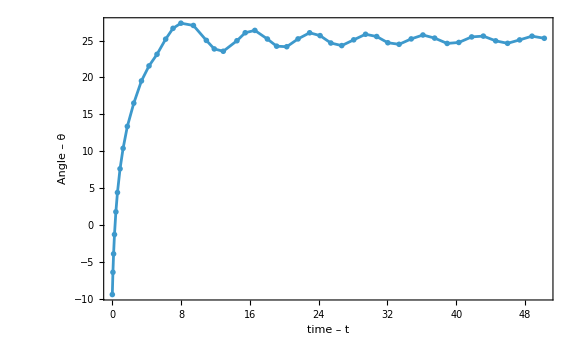

```mathematica
initialState={0,{-3.π,50},0.1};
step=updateRKF45[f,10^-2];
NestWhileList[step, initialState, s↦s[[1]]<50];
Map[s↦{s[[1]],s[[2,1]]},%];
ListPlot[%,PlotRange->Full,ImageSize->Large,Joined->True,PlotMarkers->"OpenMarkers",Frame->True,FrameLabel->{"time – t", "Angle – θ"},GridLines->{{},Table[2n π,{n,-5,5}]}]
```

## References

[1] Danby, J. M. A. Computer Modeling: From Sports to Spaceflight From Order To Chaos. Richmond, VA, 1997. Print. Chapter 3